## Thermal calculations.

#### assuming running up to the dressed - state illustrations in the bubble*.nb

```mathematica
(*Δ1=Δguess+35*^3;
Ωc =  6.0*^3;*)
geff =-.00000001;
```

#### quick and dirty finding minimum energy of the bubble potential so that we can subtract it. this is slightly dodgy since I' m just looking along the x, y, and z axes.

```mathematica
testf[x_,y_,z_]:=(*-geff mRb 9.81 (z-z1)/h+*)AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z]MagFracC2[x,y,z ]    ,x,y,z];

t= Table[{z,testf[x1,y1,z]},{z,z1-.3 mm,z1+.3mm,0.2*^-6}];
t2= Table[{x,testf[x,y1,z1]},{x,-.3 mm,+.3mm,0.2*^-6}];
t3= Table[{y,testf[x1,y,z1]},{y,-.3 mm,+.3mm,0.2*^-6}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
minloc2= Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]];
minloc3= Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
xmin = t2[[Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]],1]];
ymin = t3[[Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]],1]];
ShiftVal=(*-geff mRb 9.81 (zmin-z1)/h+*)AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]MagFracC2[x1,y1,zmin ],x1,y1,zmin];
ShiftVal2=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[xmin,y1,z1]MagFracC2[xmin,y1,z1 ],xmin,y1,z1];
ShiftVal3=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,ymin,z1]MagFracC2[x1,ymin,z1 ],x1,ymin,z1];
BestShiftVal = Min[{ShiftVal,ShiftVal2,ShiftVal3}];

potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] MagFracC2[x ,y ,z ],x,y,z ]);
potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] ,x,y,z ]);
potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] MagFracC2[x ,y ,z ],x,y,z ]);

aBox =300 μm;  (* 300 um for ZHB, 600 um for ZZH, but make sure to adjust BoltzPixel accordingly (4.04 um and 3 times that, respectively)! *)

GraphicsGrid[{{

Plot[potS[x mm,y1,z1],{x ,(x1-aBox)/mm,(x1+aBox)/mm},Axes->False,AspectRatio->1/2,ImageSize->500,GridLines->{{x1/mm},{0}},PlotRange->{-10,40 20}],
Plot[potS[x1,y mm,z1],{y ,(y1-aBox/2)/mm,(y1+aBox/2)/mm},Axes->False,AspectRatio->1,ImageSize->250,GridLines->{{y1/mm},{0}},PlotRange->{-10,40 20}],
Plot[potS[x1,y1,z mm],{z,(z1-aBox/2)/mm,(z1+aBox/2)/mm},AspectRatio->1,ImageSize->250,GridLines->{{z1/mm},{0}},Axes->False,PlotRange->{-10,40 20}]}}]
```

```mathematica
HarmonicEntropy[T_] = 3/2+(3 Log[T])/2+Log[(2 √2 π^(3/2) ((kb T)/M)^(3/2))/(√(ωx^2 ωy^2 ωz^2))];
Λ[T_] := Sqrt[2 π ℏ^2/(m kB T)] /. {kB->kB,m->mRb87,ℏ->hbar};
HarmonicEntropy[450*^-9] /. {kb ->kB,M->mRb87,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->kB,M->mRb87,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->kB,M->mRb87,ωx->2 π 25,ωy->2 π 40,ωz->2 π 40}
```

```mathematica
BoltzPixel= 4.04μm;
```

```mathematica
Parallelize[BoltzTable=Table[Exp[-potS[x mm,y mm,z mm]/kT],{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}];] (* x is long axis *)
BoltzTable //Dimensions
```

```mathematica
nKPerHz
```

```mathematica
Cloud850= BoltzTable /. kT->320/nKPerHz;
```

```mathematica
BlurValue =2; (* in BoltzPixels *) 
GraphicsGrid[{{
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{2}]],BlurValue],2] ,PlotRange->All,AspectRatio->2,ColorFunction->"Thermometer",FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","z"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{1}]],BlurValue],2] ,PlotRange->All,AspectRatio->2,ColorFunction->"Thermometer",FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","y"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{3}]],BlurValue],2] ,PlotRange->All,AspectRatio->1,ColorFunction->"Thermometer",FrameTicks->Automatic,ImageSize->400,FrameLabel->{"y","z"}]}}]
```

## Figure out what a TOF image of a thermal gas would look like

```mathematica
Ttest = 90*^-9;
TOF =16.0ms;
```

```mathematica
σv =( Sqrt[kb Ttest/mRb]TOF )/BoltzPixel (* v kernel size in BoltzPixels / second *)
```

```mathematica
TOFKernel = Table[Exp[-(vi^2+vj^2+vk^2)/(2.0 σv^2)],{vi,-75,75,1},{vj,-75,75,1},{vk,-75,75,1}];
ListContourPlot[Total[TOFKernel,{2}],PlotRange->All]
```

```mathematica
Off[General::munfl ]
```

```mathematica
TOFKernel[[-1,-1,-1]]
TOFKernel//Dimensions
```

```mathematica
Dimensions[Cloud850]
```

```mathematica
Parallelize[ack = ListConvolve[TOFKernel,ArrayPad[Cloud850,{101,76,76}]]];
```

```mathematica
BlurValue2=2;
```

```mathematica
ListDensityPlot[Reverse[GaussianFilter[Transpose[Total[ack,{2}]],BlurValue2],2],ColorFunction->"Thermometer",PlotRange->All]
```

```mathematica
Dimensions[Reverse[GaussianFilter[Transpose[Total[ack,{2}]],BlurValue2],2]]
```

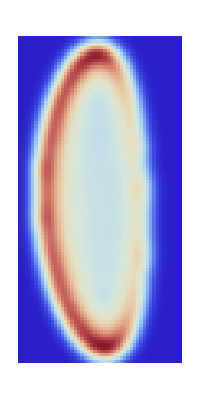

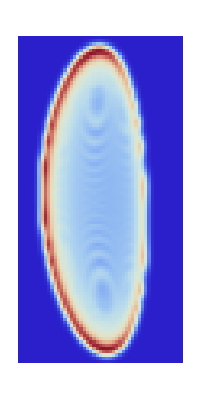

```mathematica
arrrr
```

## Calculate entropies

```mathematica
TempGrain=10;
```

```mathematica
V0 = Total[Total[Total[BoltzTable]]];
Parallelize[BoltzList=Table[{kTnK,Total[Total[Total[BoltzTable/.kT->kTnK 20.8353]]]BoltzPixel^3},{kTnK,5,90,TempGrain}]];
```

```mathematica
dcdt = Differences[BoltzList];
entropies=Table[{BoltzList[[i,1]],1.5 Log[1*^-9 BoltzList[[i,1]]]   +   Log[BoltzList[[i,2]]]    +     BoltzList[[i,1]] dcdt[[i,2]]/TempGrain/BoltzList[[i,2]]},{i,1,Length[dcdt]}];
```

```mathematica
ListPlot[entropies,GridLines->{{24},{-54.12548502616695}},Axes->False,Frame->True,Joined->True,Mesh->Full,FrameLabel->{"T (nK)","Entropy-like substance"}](* -50.906,-55.734 *)
```

```mathematica
Table[{Sort[{{-50,90},{25,24},{-5,82},{5,45},{3,56},{10,31.5},{15,28},{0,71},{-15,87},{-25,89},{-35,90},{50,20},{55,20},{100,17},{200,14},{300,14},{30,22.5}}][[i,1]],Differences[Sort[{{-50,90},{25,24},{-5,82},{5,45},{3,56},{10,32},{15,28},{0,71},{-15,87},{-25,89},{-35,90},{50,20},{55,20},{100,17},{200,14},{300,14},{30,22.5}}]][[i,2]]},{i,1,16}];
ListPlot[%,Frame->True,Mesh->All,Joined->True]
```

```mathematica
ListLogPlot[{{{50,15},{40,17},{30,19},{20,20},{10,25},{5,34},{0,79},{-5,101},{-15,111},{-50,113}},Sort[{{-50,90},{25,24},{-5,82},{5,45},{3,56},{10,31.5},{15,28},{0,71},{-15,87},{-25,89},{-35,90},{50,20},{55,20},{100,17},{200,14},{300,14},{30,22.5},{500,11},{1000,13}}]},Axes->False,Frame->True,FrameLabel->{{"T",""},{"kHz above bottom","90 nK harmonic starting point"}},Joined->True,Mesh->All,MeshStyle->Black,PlotRange->{{-100,1400},{10,120}},PlotStyle->Thickness[.015],GridLines->{{3},{15,20,90}},AspectRatio->1/2,FrameStyle->{{{Large,Thick,Black},{Large,Thick,Black}},{{Large,Thick,Black},{Large,Thick,Black}}}]
```

```mathematica
ListPlot[{Sort[{{-15,375},{-5,365},{0,350},{5,315},{10,265},{15,245},{20,220},{25,205},{50,170}}]},Axes->False,Frame->True,FrameLabel->{"kHz above bottom","T","1500 nK harmonic"},Joined->True,Mesh->All,MeshStyle->Black,PlotRange->{0,450},GridLines->{{},{400}}]
```

```mathematica
h
```

```mathematica
100000 (h 67.5488)^3/(kb 90*^-9)^3
```

```mathematica
T0  =22.5*^-9;
kT0Hz = T0/1*^-9 /nKPerHz;
100000/((V0 /. kT->kT0Hz)BoltzPixel^3 /Λ[T0]^3)
```

```mathematica
ListPlot[Sort[{{-100,4.72},{-50,4.692},{3,2.13},{-40,4.7885},{-20,4.975},{-10,4.86},{0,3.415},{10,1.808},{15,1.76},{30,2.028},{50,2.23},{100,3.01},{300,6.589}}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"kHz above bottom","PSD 100000","90 nK harmonic"},Joined->False,Mesh->Full,AspectRatio->2,GridLines->{{3,30},{4.67352}}]
```

```mathematica
Dimensions[density]
```

```mathematica
Total[Total[Total[density]]]
```

```mathematica
Position[density,Max[density]]
```

```mathematica
density[[26,12,42]]
```

```mathematica
6.626*^-34/Sqrt[2 π 1.67*^-25 1.38*^-23 32*^-9]
```

```mathematica
density = 100000 realBoltzTable/Total[Total[Total[realBoltzTable]]];
density1= 100000 realBoltzTable1/Total[Total[Total[realBoltzTable1]]];
```

```mathematica
2.612/(9.733*^-7)^3 /1*^6
```

```mathematica
Max[density]/(2*^-4 )^3
Max[density1]/(2*^-4 )^3
```

```mathematica
Solve[x  2.0/4.51==200.,x]
```

```mathematica
realBoltzTable = BoltzTable /. kT->24/nKPerHz;
```

```mathematica
realBoltzTable1 = BoltzTable /. kT->140 /nKPerHz;
```

```mathematica
noise =Table[1 Random[],{i,1,Dimensions[realBoltzTable][[1]]},{j,1,Dimensions[realBoltzTable][[3]]}];
```

```mathematica
t= Total[realBoltzTable,{2}];
t=115000 t/Total[Total[t]];
t1 = Total[realBoltzTable1,{2}];
t1 =300000 t1 /Total[Total[t1]];
tF= GaussianFilter[t,12];
t1F= GaussianFilter[t1,12];
```

```mathematica
ArrayPlot[ tF]
```

```mathematica
GraphicsGrid[{{
ArrayPlot[Downsample[PadRight[t+ noise,{450,450}],3],ColorFunction->"Thermometer"],
ArrayPlot[Downsample[PadRight[ noise+t1,{450,450}],3],ColorFunction->"Thermometer"]},
{ArrayPlot[Downsample[PadRight[noise+tF,{450,450}],3],ColorFunction->"Thermometer"],
ArrayPlot[Downsample[PadRight[noise+t1F,{450,450}],3],ColorFunction->"Thermometer"]}},ImageSize->1200]
```